```mathematica
Yb exp coil design
(* *************** *)
(* Variables (in SI) *)
(* *************** *)

μ0= 4*π*10^-7;

(* wire spec *)
a=(3/16)*25.4*10^-3 (* outer dimension of the hollow wire *);
b=1.27*10^-3 (* radius of the hole in the hollow wire *);
resist= 1.7*10^-8 (* resistivity of the copper *);
c = 0.812*10^-3 (* diameter of 20 AWG wire *);
RAWG = 33.31  *10^-3 (* resistance in Ohm per m length of 20 AWG wire *);

(* water spec *)
density= 10^3 (* of the water *);
cV= 4*10^3 (* specific heat of the water *);

(* Matt's values for flow rate: Matt used 3/16" -- 
assume the size of the hole scales the same as the dimension of the wire *)
aM=(3/16)*25.4*10^-3;
NfM=20;
flowM=10*10^-3*10^-3 (* flow rate in m3/s *);

(* ************************************ *)
(* Magnetic field in Gauss: Helmholtz config *)
(* ************************************ *)

BH[z_, μ0_, current_, R_, a_, d_, Nr_, Na_] := 1/2*μ0*current*Sum[(R + i*a)^2/(((z-d/2-j*a)^2+ (R + i*a)^2)^(3/2)), {i, 0, Nr-1}, {j, 0, Na-1}]*10^4 + 1/2*μ0*current*Sum[(R + i*a)^2/(((z+d/2+j*a)^2+ (R + i*a)^2)^(3/2)), {i, 0, Nr-1}, {j, 0, Na-1}]*10^4
GradBH[z_, μ0_, current_, R_, a_, d_, Nr_, Na_]:= D[BH[z, μ0, current, R, a, d, Nr, Na], z]
CurvBH[z_, μ0_, current_, R_, a_, d_, Nr_, Na_]:=D[GradBH[z, μ0, current, R, a, d, Nr, Na], z]

(* **************************************** *)
(* Magnetic field in Gauss: Anti-Helmholtz config *)
(* **************************************** *)

BA[z_, μ0_, current_, R_, a_, d_, Nr_, Na_] := 1/2*μ0*current*Sum[(R + i*a)^2/(((z-d/2-j*a)^2+ (R + i*a)^2)^(3/2)), {i, 0, Nr-1}, {j, 0, Na-1}]*10^4 - 1/2*μ0*current*Sum[(R + i*a)^2/(((z+d/2+j*a)^2+ (R + i*a)^2)^(3/2)), {i, 0, Nr-1}, {j, 0, Na-1}]*10^4
GradBA[z_, μ0_, current_, R_, a_, d_, Nr_, Na_]:= D[BA[z, μ0, current, R, a, d, Nr, Na], z]
CurvBA[z_, μ0_, current_, R_, a_, d_, Nr_, Na_]:=D[GradBA[z, μ0, current, R, a, d, Nr, Na], z]


(* ********** *)
(*  Inductance *)
(* ********** *)
Inductance[ μ0_, Nr_, Na_, R_, c_] := μ0 * ((Nr * Na)^2 * Pi * R^2)/(Na * c)

(* *********** *)
(* Time constant *)
(* ************ *)

TimeConstHollow[ μ0_, Nr_, Na_, R_, a_, b_, resist_] := Inductance[ μ0, Nr, Na, R, a]/resistanceHollow[resist, Nr, Na, R, a, b]
TimeConstAWG[μ0_, Nr_, Na_, R_, c_, RAWG_] := Inductance[ μ0, Nr, Na, R, c]/resistanceAWG[Nr, Na, RAWG, R, c]

(* ****************************************** *)
(* Water temp change for the coils from hollow wire *)
(* ****************************************** *)

flow[a_, aM_, NfM_, Nf_, flowM_] := (a/aM)^4*(NfM/Nf)*flowM  (* flow rate *)

(* powerHollow[current_, Nf_, R_, resist_, a_, b_] := current^2*(Nf*2*Pi*R)*(resist/(a^2 - (Pi*b^2))) (* power through Subscript[N, f] turns of hollow wire *) *)
powerHollow[current_, Nf_, R_, resist_, a_, b_] := current^2*(Nf*2*Pi*R)*(resist/(a^2 - (b^2))) 

deltaTHollow[density_, cV_, a_, aM_, NfM_, Nf_,flowM_, current_, R_, resist_, b_]:= powerHollow[current, Nf, R, resist, a, b]/(density * cV * flow[a, aM, NfM, Nf, flowM]) 


(* ****************************************** *)
(* Tot Volt required for the coils from hollow wire *)
(* ****************************************** *)

(* resistanceHollow[resist_, Nr_, Na_, R_, a_, b_] := (resist * Sum[2*Pi*(R + i*a), {i, 0, Nr-1}]*Na)/(a^2-(Pi*b^2)) *)

resistanceHollow[resist_, Nr_, Na_, R_, a_, b_] := (resist * Sum[2*Pi*(R + i*a), {i, 0, Nr-1}]*Na)/(a^2-(b^2))
voltageHollow[current_, resist_, Nr_, Na_, R_, a_, b_] := resistanceHollow[resist, Nr, Na, R, a, b]*current


(* *************************************** *)
(* Tot Volt required for the coils from AWG wire *)
(* *************************************** *)
resistanceAWG[Nr_, Na_, RAWG_, R_, c_] := Na * RAWG * Sum[2*Pi*(R+i*c), {i, 0, Nr-1}]

voltageAWG[current_, Nr_, Na_, RAWG_, R_, c_] := resistanceAWG[Nr, Na, RAWG, R, c]*current

(* ********************* *)
(* Power through 20AWG wire *)
(* ********************* *)
powerAWG[current_, Nr_, Na_, RAWG_, R_, c_] := current^2 * resistanceAWG[Nr, Na, RAWG, R, c]

(* ********************************* *)
(* Water temp change for cooled AWG wire  *)
(* ***********************************)

deltaTAWG[density_, cV_,a_, aM_, NfM_, Nf_, flowM_, current_, Nr_, Na_, RAWG_, R_, c_]:= powerAWG[current, Nr, Na, RAWG, R, c]/(density * cV * flow[a, aM, NfM, Nf, flowM])
```

coil design exp Yb

coils MOT

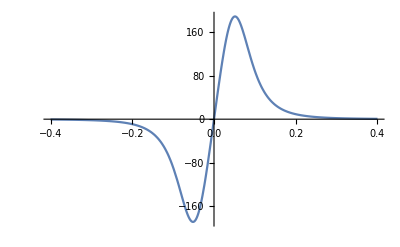

Bias field in z-direction (G): 243.603

Bias field in z-direction at the table (G): 3.94623

Bias field in z-direction (G): 0.

Gradient (G/cm): 54.5565

Curvature  (G/cm2): 0.

Power through coil (W): 305.135

Voltage to be supplied (V): 30.5135

Resistance per coil (Ohm): 3.05135

Current per coil (A): 10

ΔT (C): 0.122216

Inductance (H) : 0.0324851

Time constant (ms) : 10.6461

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 120. | 132.992 | 23.548 | 232 | 70

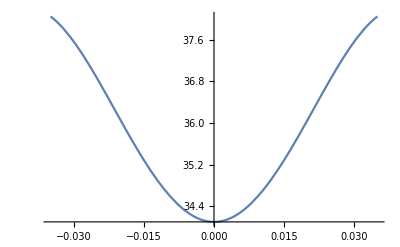

```mathematica
MOT coils

(* wire spec *)
c = 0.812*10^-3 (* diameter of 20 AWG wire *);

(* geometry *)
R= 60*10^-3;
d= 70 *10^-3;
current = 10;
Nr = 6(*turns in the radial direction *);
Na = 20 (* turns in the axial direction *);

(* water cooling system *)
f = 6.33 * 10^-3 (* size of water cooling channel--take to have square cross-section *);

Plot[BA[z, μ0, current, R, c, d, Nr, Na], {z, -0.4, 0.4}] 

Print["Bias field in z-direction (G): " , BH[z, μ0, current, R, c, d, Nr, Na]/. z->0  ](*Helmholtz config bias field in G *) 

Print["Bias field in z-direction at the table (G): ", BH[z,μ0, current, R, a, d, Nr, Na]/. z-> 0.4] (* bias field at the table*)

Print["Bias field in z-direction (G): " , BA[z, μ0, current, R, c, d, Nr, Na]/. z->0  ](* bias field in G *) 

Print["Gradient (G/cm): " , GradBA[z, μ0, current, R, c, d, Nr, Na]/100 /. z->0  ](* grad in G/cm *) 

Print["Curvature  (G/cm2): ",  CurvBA[z, μ0, current, R, c, d, Nr, Na]/10000 /. z->0 ](* grad in G/cm2 *) 

Print["Power through coil (W): ", powerAWG[current, Nr, Na, RAWG, R, c]]  (* power through coil in W *)

Print["Voltage to be supplied (V): ", voltageAWG[current, Nr, Na, RAWG, R, c]]  (* voltage in V *)

Print["Resistance per coil (Ohm): ", resistanceAWG[Nr, Na, RAWG, R, c]]  (* resistance in Ohm *)

Print["Current per coil (A): ", current]  (* current in A *)

Print["ΔT (C): ", deltaTAWG[density, cV, f, aM, NfM, 1, flowM, current, Nr, Na, RAWG, R, c]](* water temp change in C *)

Print["Inductance (H) : ", Inductance[ μ0, Nr, Na, R, c]] (* inductance of the coil in H *)

Print["Time constant (ms) : ", TimeConstAWG[μ0, Nr, Na, R, c, RAWG]*1000] (* time const in ms *)

TableForm[{{N[2*R]*1000, 2*(R+(c*Nr))*1000, c*Na*1000, Na*Nr, d*1000}},TableHeadings->{ {} ,{"Inner diameter (mm)", "Outer diameter (mm)", "Thickness (mm)", "# turns", "distance between coils (mm)"}}]

Plot[BH[z, μ0, 1.4, R, c, d, Nr, Na], {z, -d/2, d/2}]
```

coils Field High

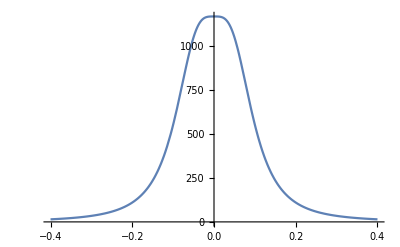

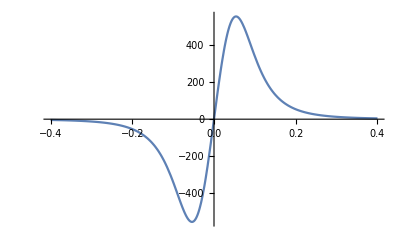

Bias field in z-direction at the table--Helmholtz (G): 14.6306

Bias field in z-direction at the table--Anti-Helmholtz (G): 4.24885

Bias field in z-direction (G): 1169

Gradient (G/cm): 0

Curvature  (G/cm2): 0

Power through coil (W): 678

Voltage to be supplied (V): 8

Resistance per coil (mOhm): 26

Current per coil (A): 300

ΔT (C): 17

Inductance (mH) : 1

Time constant (ms) : 41

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 145. | 195.292 | 25.146 | 36 | 62

19

```mathematica
High Field coils

(* wire spec *)
a=0.165*25.4*10^-3 (* outer dimension of the hollow wire *);
(*b=(2.5/2)*10^-3 (* radius of the hole in the hollow wire *);*)
b = 0.09*25.4*10^-3  ;
resist= 1.7*10^-8 (* resistivity of the copper *);

(* geometry *)
R= 72.5*10^-3;
d= 62*10^-3;
current = 300;
Nr = 6(*turns in the radial direction *);
Na = 6(* turns in the axial direction *);

(* water cooling system *)
Nf = 2* Na (* turns water flows through *); 

Plot[BH[z, μ0, current, R, a, d, Nr, Na], {z, -0.4 , 0.4}] 

Plot[BA[z, μ0, current, R, a, d, Nr, Na], {z, -0.4 , 0.4}] 

Print["Bias field in z-direction at the table--Helmholtz (G): ", BH[z,μ0, current, R, a, d, Nr, Na]/. z-> 0.4] (* bias field at the table*)

Print["Bias field in z-direction at the table--Anti-Helmholtz (G): ", BA[z,μ0, current, R, a, d, Nr, Na]/. z-> 0.4] (* bias field at the table*)

Print["Bias field in z-direction (G): " , Round[BH[z, μ0, current, R, a, d, Nr, Na]/. z->0  ]](* bias field in G *) 

Print["Gradient (G/cm): " , Round[GradBH[z, μ0, current, R, a, d, Nr, Na]/100 /. z->0  ]](* grad in G/cm *) 

Print["Curvature  (G/cm2): ",  Round[CurvBH[z, μ0, current, R, a, d, Nr, Na]/10000 /. z->0 ]](* grad in G/cm2 *) 

Print["Power through coil (W): ", Round[powerHollow[current, Nf, R, resist, a, b]]]  (* power through coil in W *)

Print["Voltage to be supplied (V): ", Round[voltageHollow[current, resist, Nr, Na, R, a, b]  ]](* voltage in V *)

Print["Resistance per coil (mOhm): ", Round[resistanceHollow[resist, Nr, Na, R, a, b]*10^3]]  (* resistance in Ohm *)

Print["Current per coil (A): ", current]  (* current in A *)

Print["ΔT (C): ", Round[deltaTHollow[density, cV, a, aM, NfM, Nf,flowM, current, R, resist, b]]](* water temp change in C *)

Print["Inductance (mH) : ", Round[Inductance[ μ0, Nr, Na, R, a]*10^3] ](* inductance of the coil in H *)

Print["Time constant (ms) : ", Round[TimeConstHollow[ μ0, Nr, Na, R, a, b, resist]*1000] ](* time const in ms *)

TableForm[{{N[2*R]*1000, 2*(R+(a*Nr))*1000, a*Na*1000, Na*Nr, d*1000}},TableHeadings->{ {} ,{"Inner diameter (mm)", "Outer diameter (mm)", "Thickness (mm)", "# turns", "distance between coils (mm)"}}]
Print[Round[Sum[2*Pi*(R + i*a), {i, 0, Nr-1}]*Na]]
```

Bias (coils:biggest ones the X)

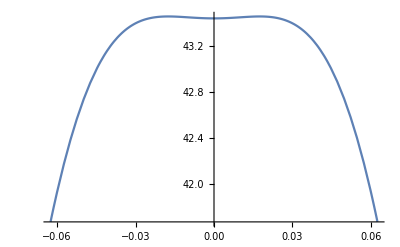

Bias field in x-direction (G): 43.445

Gradient (G/cm): 0.

Curvature  (G/cm2): 0.0221721

Power through coil (W): 118.745

Voltage to be supplied (V): 16.9636

Resistance per coil (Ohm): 2.42337

Current per coil (A): 7

Inductance (H) : 0.0683701

Time constant (ms) : 28.2128

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 250. | 266.24 | 7.308 | 90 | 125

Cell[BoxData[

 GraphicsBox[{{{}, {}, 

    TagBox[

     {RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6], Opacity[

      1.], LineBox[CompressedData["

1:eJw12nk4lN/7OHCJLAkpJFIkJMmWrTiDGansW8quKBKSPYQkW8yMMdbsW5QR

KqSOyhZKSdZIsr1VkiVL0vecz/X7/cP1ujzzOOd57nPOfd+IOXuZuTAzMTE5

oS/4uxwQmPn3jwFpHN18uh+JBK/V/TGraww4/J+uWSdyZbWC5MISAxb7Uh0s

e4kERWlD58lvDFgv2/3VtY9IUN0eNdjZx4Dz744m3x4gEghff7WnMxgw3eQK

GQ4TCWa335QrOTBgylitCOckkRDQFXXl4vMK6CEYa8z5m0jo6dk688LpAeyy

N1YUFiAR9jR67VQVuQ8rMvyzRuVJhEeXm1h5hsugovMDM219EsExQWFuIPIe

VL5y2ynOnkRYoV6PgaAUHj6vHJjuTSIUcI8IpX0phg7BBzfsIkgEqg1gU/9U

DCVZp05nIEeW5i4O9BbDvTemvXqRnXXOdwl3FkPbhu8aRpEkgrj/dFTO42LY

7Hd15NhNEiF/eP5ncXwxfGt+5CLPLRIh9z5by6OjxfADu9ZIagyJkHVKwedD

bBGc3XXLWSGJRJDYeqr9XVQR1LvtbeCIXN7hLP72RhFcYWfnT0KuN6B1t/kV

QcXNbjrfkQeMlhWfOxVB3/NKPEVkEkHA/NlCqXoRHNFbDOalkghJNif9wv4r

hA18vd/e0tD4PZwCD54shHviZ599TycRRhLts+p1C+HWkpAlgQwSQeOhTeNp

rULYf/kEhzby/JIlu6dSIQxS72qmITvdOJVWtacQ3ica0TQySQQCVan22HwB

tPXXod3IIhE2nrCuGGYWQOY9gnE/s0mE65vLAnx+5MPFTdH57gUkgme6/RbH

6Xz4IXh4fxyy85EdKYZf8+HYTpvYe8inbEKqpAfyYUntGtM08q5qox8jTfmw

R1Gm8HwhiVDjvOB8OisfAgPQbFlEIsy+OG4kcTofrkiyth8oIRHGzvz6tF0v

H6bOXZzWRv74o+jyP0I+rBSN/G6H3CDEEzuokg/PTHMXpyDHX/3yiiyeD+U2

/vu8uZREkBaLVv+7mgc7NIqChpCdwrskekvzoPYHubsBZSSC1UCO1nBBHtRz

i9tGRj6l6G09np0Hp4YOuJYiK4/zJszT0PVPTr/rR2bXN1vgjsiDO8eyY9XK

SYQKno8vTpzNgyVBMGMB+U/2oH0dRx7MsngVa/2ARJhbLgtsZMmD8jycQp7I

4ybXqa3/cuE+w63Um8hvmUVaPi7lwnqah3YFcr6r3eH5L7lwg22JzlxBIujL

jf6Rqc+F9OdXpUqQU55NpGW550Kernz5UQaJYB+YEabqkgu7t5SULCJLKxlf

6HbIhbHO8ls4KlF8ldYeYbfMhaOx3MEKyCPJ8S3XQC70DsvSikCWcldYPLUz

FyoO79YXeUgi+Bxey56/ngP3Vek1E6pIBJaC8+7SV3Og4IUfJ82Q6bveHLV3

zYFzustPziM/3Zzb+dokBx7742USja8fJK3lHsiB9D8033Z8fTTF0rgrG/4W

KqYbVaPxfJbmui+eDS3Hzt3TqyERQo5vepCxKxvmW+wPtkDWTB8wjOXOho4G

vWrOyI1mcUmua3ehx5VD4aHIrc3f+MS670IC+bNqNXJPeYUQPeIu5Ir8YCn8

CMVPgLJU+GgW5L7/LHsEubKHq82zNwu+8HmjO4N8VWHikl1nFnRc1u5fQl6c

SSnTqM2CLYIxXVyP0fuzWz68lJQFrS68W1FHZifWK7uDLCiwKZZAQd7PS9Cx

yM6EFjV/lpSekAiJ8l+C3ZMzoX/3ritayCsmkdXhMZnQIORStz5yJ6VJ4oFP

JgxbGbhoh+y74yTblhOZsD4nG95CbhEw63zyMwPenbty5AOyvOoCy9vxDLj9

YSz5E3LGGZrm+EAGTOxqHJ1A9krrreBtyoDiy/VGK8i7dttQ3NIyoOE/H2eR

WhLBfc8FK2HtDBicGuPnhNyjyZqkoJIB9UN2d7kha9kXt544lAHNih7s8kHe

kTOt5sufAeW7eUMikRv2XRF+81861Dp59lY+MreE/2gYNR0OP7Or+IxcJRPj

PvY1Dboe/NJgVEci7H3vWHdoIA1a20/tsEROCFBn93ubBjWGle1skF2aZorY

6tKg/d7BlovIu+wNv8gmpsGR10+XbyCHUvisA9TSYLGz9tAD5BnVb8WNh9Mg

n/mAbTWy1cirJY79abA5P+Z9LbL8Ib/krG3o8z8caa+Qx5r63r4YS4UBJo4R

/cj6K1kkrjup8Hl+12amenReZPvRLCNTYcLn0QYWZHGS0dfsgFRoLtTrxoH8

h/IvXME5FcYdzsnhQ6445NxgpZoK3RnbQiSQdzpIKeV9ocPgMvvNesgRrEyR

M710WLmUynQKeba8/51SJx1Wq4TNGyK3rsR6tjymwwSLmzWWyMHU7/e+xdOh

v3ZH1QXkz80P96mo0OGcxt6CcOQQ81Wimiwdatvo195E3vWF4KYhTocxrTpN

0cgm610PtbjpsJH3Q2MCcqPirM6JyRToneJnmIacmyPjYk1PgVmjZ589QD5+

2Cf2XEIKZJ5TIlYi99fXPbCNTIENwiEvq5B5e/V/O3qmwNGk0KIneD5cF2+7

6aVAWGm+5QWyc1DBveDfNLh4t/ZYN/LGlm9vQr7TYLThqmYPcgZNcT5sjAZV

2rTVepG7GS80br6lQY3dvPyDyLqTnzvii2kw9Gy59xfk0WtSc3eyaFAvT0n5

K57vJq+dZCoNfrLkmRtHrhHZsKWF0WBb6qTJNLKEuchslhUNTjbvrp3F8x09

z5djQIPa3UQwh2zrWa6Sp0OD3ULb4C9kWqzGjSI5GjSKvFu6iMzSaM1bsYUG

d/K9kFjDz8cwV7lyPRnOXRq9+gc/n6Ep66r5ZFg8P/VkHdn3t3/e45FkOHm2

R+4f8oRsiiJ8nAz39Ym/3vyURJAJK5qdLk+GjWPlSyzInl2PyvjykmFCh9Lu

LcgrV3vFXeOTIcdNz9PsyMdfTY4khSfDeQ81aw7kiJ3LGXV+ydDZ/YgdJzLn

E8Ed2xyToVxetzEXsjG7dJeKZTLk6krR3IZMO6sW73gqGYatVu/nRt6zbr25

RjkZUpflBniQ5bUzFs5xJEMmL/sZPmQ/ahkjaoMKfwSpZe1Arv9af7ligQrH

L7Xp7UTWjR76ummECtfZVaP5kWP6vuUc+kCF9WqywgLIndLrNpZtVFhzkuUe

tlWHSE9pFRU2fYxlCCJniBwmd5dQ4a0SQ+ldyJ+vaBqsZ1HhIJtYBrYENGSX

pFJhIj8PqxDyJV77JuPbVGg3I+6G/cDJMzwohAr/ZlxswZ6vCjtecJUKeVWn

RXYjq7AkrXS6UqHMa4YH9nXLnJrfNlTYZvX6EXZjMcN7nykVnhkFK9gsK1D2

lB4VSjiJKgsjnzz5bvraMSp07fJyw07MGC28K0+FyiIgDbv725xj6wEqTFBK

bcQW1Ny059duKjy2HjmGbZu4fWA3L3o+Z7ZtYOd+FkshslKh5X7tHSLIE/KK

pp5rFFh29KA4tkykzra0nxSo6PROBtvzg9nrF+MUOOejfRi7WuL8rW8DFNio

ePsg9orfNW3+LgrUP39/L/bx1pt/tZoo8PeLpzzYEbtodZfqKJCFrXEV//4W

t0I/agUFek68Gsbe+rRGoaGAAtc4u59im3A1/5hIo0CZfUvJ2DS7j/d4EilQ

u03VFXugYsJF/SYF6uQVKmKLMv0WOx9IgeO6eqv4+TmbbhlJuEKB2bpS9djf

FyStRs9QYOmd9zLY8iRVPk5DCnQdZwzi9+VHP/FWSYcCOR8uR2FvqF3Suy1L

gZZxP9rw+9eNC2R+KEaBbwMrnbFjhmKeDwpQYEfulmUcP9vD7qnIbULzk6Tz

YEc/lm7jXSbDr4uns3C8rc2WnF34Toa7HC5LYI85FIfU9pNhwG12KRyvVdoF

L3UqyfB5V9FvHO+SweIWB4rJMEOT6oCdUZU3wZZFhg2fZZq2I0fuz2V/c5sM

3z6PCOdFNmO9a3TGgQzVfpW34PXVoikyqm5JhiZSo9uwNfwzr4qcJkNXMWZT

vB7Fp9JpX1TIcGbgSAderwtt9MHL3GS48XQnmQ1ZSkjsDdP1JNh5geM8EzJv

3N65ZtckaHbsswfeP1bW9uyIN0uCsm/Er20gt33afZZfJgnS4vn88H5zKXfn

xMGBRDji4GW8glwmxf7XTDURDuZOXfiJLKvyU7ZoIQFy9qvqDyG7yt24UTec

ABmuZe8HkHMkebrftCbAuTAO635kPsEjAb8zE6COX5XNR+TlZc8XJ4gJ8LJW

FehCflk3azlDi4fMApcjXyJba86GHVGJg2OhMQolyDeJP97VBd6GnyQHBC8j

81tUkM8KRkKqwxaOH+g8rZKMrydtjoQRcRZq35BNVi+OK/yMgJUl2pf+Q47L

FlPjbI2Av9S2tk8gb0zTPtf7R0B9iU8pI8iTodflRHrDoZnVJbN3yJ7GlLRn

B29AgUYYWoNcunjqe8qmG7CxL+p1FT7P01kIngNhUO7qNYGH+PwfD5gSjQ2D

0oeHq3F+AILsVcKnQ+FKu+nfYmTegkM9OiUhMEpK6m06Hu/vZp42iWAoce9R

RDhyYln+S63VIJgUf2AgDPmy/Q2/R2+C4GRrmGIoskSL2lC+fxBcDNqYCUKm

p5QXh7YFwjdu965dQw5WpmgqeQRARvDpKVdkHR/by9nVvtDxwvFrxsiikuqi

/DG+8ORSPg/Oh/4M8L+Pt/WFGk89KwyQa7S7VIJYfWFplO7CSWTJ7TrMFmeu

wej3IIOIzFkplc7x5yocmTvrqIFcNDRx578oT2ihajImhTwYIpBzV8kTWnX4

fJVE5hY9UWk6dgXydm9MHkD2dyztrgNXYLyzzdJ+ZL0Jd8G4tcvQM8b+yD7k

6dmfuTLebpCQp7FbCFmEvK9qRNQNNrKO6OzC71PB9BX1zSUYzcnhKYhce61q

Yk3mEgyH6x38yLErvjIdE67QVTa2mA9Zhnmt+rLNBRiXTe/jQrYvkGney3kB

zp3xPYhNJdr0fqg9D2/ZzIduRV6Lblg5JnAempb1yHEid2y9ocn13gkW8pyp

ZENmesAwarzhBDNmbASxlY1GHXzlnOCE6daILchZZO3IT/GO0DrU05YVuV+G

PfHsHXt4Zper0mZkwhW3yhczdtDD8DODGccTo737oL4dvDa79Qh2kPIdwTVm

W/gu+ObRTci7tfjyMgLPwnPVW87/Q/lsZPi1V8y91tDDRWVpA/nby54JdyVr

KMokFofdcCJV5tisFTxBlGn4i2xnKlIzdN4Czonv116vxfvnkrpfkznUclmY

+YMcQu+C3AfMYfgxt1TsrKHIDu1JU1i7T39lDVk2zNZ0SM8UGjlV3cd+uk+l

z7fEBHKlN53HrunobjZ+bwQ7dn0dWMX5O2/0+0iqIbRwm0vDXrBUH35kbgBF

X5acw1YczVkU7j0JOVwEJleQTQ+YMxmn6sPcxLcMbG/3LVyR1ieg6w3FEGzG

osf+6UEiHD3+TwT7rfq+I8JZunARXvq1jDwb9kHDyE4HLvrfaMPe1hStFyGq

DZUrdfOxrfl8Cy9BAH/WPArDTs0afPpWWxMeef3RDrtXUvuDcpMGnDlUCLB3

PiyZydBTgxMCYhLY5se4mTe9Pgo7nxtsxaY2+wpdPK0E95lLLf1Gfmc8JP/m

jTwkblR+wRatuUl2zZWFvhP/vcPObDOBikVSsF26+yX2ruE9sxv3xKHWV7cn

2Ie+flSn2wnDfJmHFdiSXN6pche3o3grLcUO75HuEX719/mHu0ZF2LI8w+6s

h8e1aEOFhdi9vyJzeFfYweH2smLsOWOpeS8fAfDCxbEc+3qyXvtl5X3gdFFz

FfZGWFBmzpEDoDR4sOF/93e/7/FBRgbEdme/xt5s9VmTTfIIuE3jG8B+tS/2

9l1eRcBdcPQbdhRd3Fs1URl4DLEx4eehx9Vg/X6rKujgjxXEZou01L4cqw5k

D9QpYLctzx5kZTsOfPtSjbDjrsTw5URpAdslCU/s4l/kUJEIAojWcSRjX7wo

4/p4QwdYOYx+wtYXDzh3U5MIwrIk2PD7lx5+ZWQSQgILX/mVsWfM7FRnVk8A

ovJGCnb7trJDT9ROgjsRi+3Y5W2/90YFnAIbTnRmHH8eWmR20SUDUCo7FIRt

uPppfUbJCKih3RVbrubgryc+xiBr0+s/2Cu0L9+lV0wA+7pNDI73Os7rH1/6

mQMTJccXeL3kHub/wBC3AJPXaHvw+oo2YbzL6rIA9OqJEGwL+tcO/4NWoKh9

iIjX45yYwUuZYWsgz/x3Fa/XPuIkFIw7C9h3MXnh9f38YvgzFtVzYKV01xR2

/IOa2hGyDVBbuDXKhPdj9T0MKtEeNGUprOD9gsv2yf0bv+xBt/yLW3h/WQgz

LfPIdgCBS7YCLMiOYy/N9oc4gtDxagLej+Sklw3/fnQCpal1dXj/el3tQHwY

ewGwM38+tg35eLPsK6nRC6C59fYqdmXvqna2igug90nUc+PzZjUZxH91AUzj

ykRe5AugTcNF8yJIjA2+vgP5X7u8gtAvN6BXuOC7G9nn019G0gl30C/C7CSM

z9cf7XJbst3B94kJYxHkTl4X2YVTl8G+GgkVUeQMq3SpN4UewKSRICGOfHRs

k2iEtRfwD5qKksHjrz/zS/6eF/j+6WLcIfw8qA+aRle9QOesFlUWeWve/aO5

ht6gP3u6VA553cT6079ZbxB558cvReThSsZBqOADTu1tnTuGnONt36T5xBes

Oc6S8fmYZctRkfLZF5Q1vfxkgpymX5P6g80PiL/MkTFDJu/jvHzX2g8Uu1zq

tEAOf/do+99VP1AoOSF1DtlJfptDw/EAcHkb83EX5P1zT1c1XgaB3A2nVyHI

IW90oxZ/BIHffTaX8fneW9bBXSEUDOjuRH58/se5DO0XuxoMtJTeed5Enhtc

M2Tbdx08ZrVSi0N+3qye/yE0BOR92CeWhnwu88kpD/UbYG35ivQj5JMFA2+M

rCPBd8+o7/PIJEO+zUuPbgNrZtc73ihfSnTi+LX6+jYI9E208MH1th/T543h

2+CY0dvdvsju2bP17FtiQL5xSGEAvv5nu4+IVQxwlPmvPAxfT7k5pvs7Buw6

WXML1/fuvYsvqCpxQPskVR3nZ9Uz3xipp+KAxnBDXyny+sbY3Sz7OCA/o+Jb

hu8n9T6oODoOBBL/leD6vzrwgUJ9bxzw6ZNeq8bX73bN++IfDzw/8+g2Iic5

9IXLP0kAnHrtqn3I0d+Pg8nOBCDYIFCJ88mwoPy/mWMJwLTT5QCu5z2TrwSz

cd8BVPLUlmFko9bNviMX7gAdxeuFY8jcR+QvJvAlAo3eIe0fyFsaUg7oSCeC

i3Xs0bh+39D/83VZMxEYfylswfntrHOL43m3ROBnx6o5j/yWbntOozERtFja

//2N57MRYzh9JQn4dws24Xw6On52a/bNJKAm2NSO8+2wXRbt5ulJQCNU780m

XH8p7j0Bm5LA7qziZlyvS1Wf29exjQxEfV5E4ny9IOjOv6JdZHDjKNdFXJ/v

JTSOhO8nA1+XET1cnwu+OXBXRZ0M+km/VnC+zzY1J5R/gQwq3OsO4Pr75oP9

qyFe6H4i0hPY/65Z9Z8JJoNI0bc5uB5fZmqgbyOTQW126hZcf1xrnfWbziCD

f93FVdg/74hZvioig0PNTWdxvTK1+/aOoKfo8ztY0nG9fv5L3bx5CxkIrPEq

4Hr9c8n393LvycC9enMTdp+yGXl8kgwm/a8O4nrI/E+UF/xFBlWf++xwvdT1

4olRxjoZUPvXhrBbjfZsM+GjgNk/Bm243top90XAR4QCpKngCK7PHLcV7aNJ

UoCvbSAFe61DVrlfgwIEYjJO4PpOr3xOc41IARmffDKxk+NqTogYU0DKaa8Z

bNmTx20cz1OAp2JVEK4XA6WZXCKvUMBoyFQddjNbk2dhAAUsRosuYfNN3Q5s

iaCAXobRIVyP2recjpyOp4AcMy9b7LIingROOgVcaAmIwV6O+pAim0sBcvYO

DGzihdQcozIKYHHb8x6brGtzz7uGAsYV7v3A/iS+t5r6nALe/ltlwfX0Qeav

DTVtFNDAzyaI7f+luKW3mwIqqlr3Y79sdH+38okC8rcrHcLmyZUb3D2F5udG

+F/9bntj/uvxXxRA/zH5v/q91P7xD/s/FFDVuUcMe0kzeDmclQpYFD/xYevs

0dpUwEMFZUShf//rP6xv2tosRAUfpTonsIeGmndO7aeClrVvLdjST2NFOeSo

oKnfKx/bN8NQ+pAaFSgMGAVivwjarmioQwUhPOH62NxnPx7zMqACufg1Puxz

aukkihUVjJ151Iefb7GgnXG1IxWcCi2hYy/83nf2ozsVqP9rNcYm9I47L/tS

AX1422bshEelHkI3qMBjp3clfp8DNA//Y7FUMJI5cQZb0lc+3C6ZClQuuazi

+ICKtcl5JVTgcsdBBpuLL+Tuq4dUEPa0tQ7Hl/UvUDLxlAo4Bvh1secZrfUH

31FBhTPQxfGolRTfdHqQCs7dYq/H8Rvvafz2yjgVpLMky2BLHO778nCFClZs

WlfwevDmyvz2gTkZHO60t8J+9s1+aYkrGex/TX2A149V2SS7hlgy6PQq18fr

Kz+2jM/2UDKwSg5NwPX+z0ueImFHkwFRtfU1Xp8xUr+PvDyZDPLbM+Xx+u3Z

Uq8+bp4Mhvh3nsP1v9hkqO4W+2TAkz4Sguv/+kLWM6d8ksH8R2IF3g9+iPGH

dWckg6vAGOJ+n9r1vKsvCpPBwfeMJ6y439Bz2KWyIhnY7Le7h/uDArf1DBJf

JgMBi+BAZjz/7wG7T80kAz2Vpqa/aD+LIbFwqy8mg++K5GjcD+jOJm+S3kgG

BnJO2rg/6Wp6b5qVjwbuM83m4f5A0uPBxy/UaeA/v0fbFpAHeS6WVerSQNOX

cjruf0q4LdzNMaQBlkf2u3B/tFaY61aoEw04sn1kxfvxaLimuXosDfwY2hwz

iaxwOvdnZT8NcGbbiOH9PqRQ9mvOGA38TnitgPu5LX9rexO/08BVbUcN3O89

V/n+mQdTCiDmjym9Q47k35wgLZ0C6iWOtrYif/jsIp0bkAJuTX90fYQsqj4v

nBSRAgaJbku433yJGsYTFp8CylMTr+N+9Dox9bdNTgqIZnLzLMfjL2trEmxN

ARpmpj9ykf18DzklCdBBxd3YE3HIApw/G6zE6IDMo8VxG88vp2qXqCwdtDgb

N+J++Xq7+rv72nTA+c+KOxSPT0wftHvQAfulu9Je+Dx5e2EP6ys6CIzaedoU

Wf6CdFDnGzow0m2wxf3696vfepL76cD2zIrzSdzvP3AtQXwW3e/9moE27ndf

j/gDhFJB/5XmFHnkYunsgWCvVJBed+InF7L+c6ejOsGpoNnpOJEd+T/zAxSO

W6mAOrWSsBn3c27c10/LSAUm/6WsruL+xMf6J4+aU8H9iCXNSZx/RPalzAmn

gYzu7xcbkPs+8Zq5tqWB1xVcE/bIp+Jd+n2708A9gx1bziI3qNfb3/yUBjz/

cQibI+fSz1/OnUsDl3Sz9p1AvmTyOGpwVzr4uVMiHedra69snhi5pYNFEVUV

nF+LlBeLqHJmgLQrmR/ikBPP/skn7cwA85zX7G4iM7GbHLQQzQAh7EMD15HH

L6wevaqYAYITj5R5ID8QNTAuP5cBnI5UlRjivydRf0XsLc8AvVWmXNuQHYOO

T7EZZIIKXcnDEU9IBJkLbR9nrTLBoCufbADygpFF00enTDAuEy90BTlawiOv

ICATKLtPQ2vk+12ZNqAgExit16kdQV498KfLfy0TtOrOv+l/jOrF7rraidIs

kBW4uFcU2fYZqaSzOgvo+/L3bEc+UPo+pfp5FiA/+u7Lilwb+p9PRE8WuJQa

GfL9EYkwIi10eA/TXTB9rDyvDlnmRmCexZm7ILfqq4oJ8qtDqnGvWLMB9bew

hGcNOq+OWBT84skGopLrho7IK4pXG/buzgYdiW4uZsiyGuWz1+WygWt7va0K

Mk1/r7nymWzwsnv48t9qtJ5d2ESKSrPBSp/1phhk9py+B9Gnc0C/s09VYhXa

v/IXW2osc8DNQBb/MOTjxdtHxxxywJpS6gFPZO8Hp/mAbw4YfpKgb4g88BT6

L2flAH//c1mcyGX9JeDSbA4Id6F4RzxE+zdHw3Shfi6Aiw3XHCrRftwq555v

mAvetQ78NUB+Hp33LccsF4g8O35NA9mK5fZshm0umEgt2suPfOuf6SLZOxfE

lD4Ofc1A739p6l9IWi4ofO1NlEPOH9shaDmdCzibV0qnHqD8Ky86zexHLtAR

fhfVjazhuCpkMp8Leu57n3qG3D08InJ6PRe0vRimUpE3DdwT1+bNAyrnhASP

Izt2AbnDanngpFb+WNx9EmFPw2USa0weYOSfVBQsR+tRaG3N804euMsRIPm3

DJ0//jGV/VT0eZnnG2PI60eKhO/fzQObrtvaVCAPFoz8MqvOA/VRh1/pItPj

TbNzR/LAe6WXwO0eOk9tVJePHc0H82eeRWSXoHhfY77nM5YP9Ndfva8oQOP5

OrBwYyoflCx8ISchN3ZWat35ng8sChyVvZHDc+x7Sn7nA6d6I2kF5H/E+n+f

OAsA87vklw/zUb6bdNXqhFIBiPq28OhBHhrfgdHNIlEFoJ38Upucg/Ib02f2

zQcKAXnlj+bfDLRfDTCGtQ4VghnzrKAPyNxO+ba18oXA4LUC5R6ypPftc+XH

CoEN2DC3RLZINLWimBaCHpcrkuXpqJ5snzC0Cy0E9X0yv4zTSAQ3XW7NpZ5C

YHjycVVoCso/lB2ED0QVgTZPL4prEorH1aM8t2KLgHKll7Yy8twzrs0TiUXg

qi1HxyZklhP1M4XpRUCC/s49KxHVh2f56yUYRSAxXGKo6w6af2iHtcQg+rlw

hs+RBDS+FlX6fvliUFbPKvw+BsXrGd7t4p+KgXCnpWFmBIkgRBu3ZtlTCh4G

Sb4+70MiVNjkliwE3gNr4S6jYg4kwhnNG/ptz8rAcUeVDpdTJMJD+yviGuvl

oEk3sNFaCa03Tt3NdZYPgOZKprWkIIlg9v6Yyp60ClC6bVNuwyqRwHls64uG

uxVgx36ps4rILwoHT9sWVIDj1I89JStEgnxgkFNmRQXwrX24g7pMJHDvfZIg

1FwBwig1FeeXiITXHopf+ecrAEHnssWfOSKBwH6QzG3AABT7eOX1KSJh5erK

7gpTBqg6/FnRHZkx1FpkeIYBdKX/zvdNEgmiDNenCc4MoMMbWVs1QSSsWxZO

cgYxQH7WbmuXr0TCk4K9mmzFDFB5dG38+QiR4LntZ2txOQMYpF3/K40sGfDc

TO8hAxS0+vZRh4kE2im7S7caGGBy39Mul09Egs+vjOTNHxiAXrH9PfsgkSBj

4y5a0M8Ajw51LHoPEAlfmtTv6YwwgGlY70B/P5Fgktb/POI/Bjhp8G6qpI9I

YGcuPSn2kwHcHz7i5UGGlwN6GhcZ4A4cXPPrJRL8P+o5OK4xgOqmY8WfPhIJ

/+//v8D///+v/wMIJXVv

       "]]},

     Annotation[#, "Charting`Private`Tag$3182#1"]& ]}, {}, {}},

  AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],

  Axes->{True, True},

  AxesLabel->{None, None},

  AxesOrigin->{0, 41.66610942130788},

  DisplayFunction->Identity,

  Frame->{{False, False}, {False, False}},

  FrameLabel->{{None, None}, {None, None}},

  FrameTicks->{{Automatic, 

     Charting`ScaledFrameTicks[{Identity, Identity}]}, {Automatic, 

     Charting`ScaledFrameTicks[{Identity, Identity}]}},

  GridLines->{None, None},

  GridLinesStyle->Directive[

    GrayLevel[0.5, 0.4]],

  ImagePadding->All,

  Method->{

   "DefaultBoundaryStyle" -> Automatic, "DefaultMeshStyle" -> 

    AbsolutePointSize[6], "ScalingFunctions" -> None, 

    "CoordinatesToolOptions" -> {"DisplayFunction" -> ({

        (Identity[#]& )[

         Part[#, 1]], 

        (Identity[#]& )[

         Part[#, 2]]}& ), "CopiedValueFunction" -> ({

        (Identity[#]& )[

         Part[#, 1]], 

        (Identity[#]& )[

         Part[#, 2]]}& )}},

  PlotRange->NCache[{{

      Rational[-1, 16], 

      Rational[1, 16]}, {41.66610942130788, 43.461797387082584`}}, {{-0.0625, 

    0.0625}, {41.66610942130788, 43.461797387082584`}}],

  PlotRangeClipping->True,

  PlotRangePadding->{{

     Scaled[0.02], 

     Scaled[0.02]}, {

     Scaled[0.05], 

     Scaled[0.05]}},

  Ticks->{Automatic, Automatic}]], "Output",

 CellChangeTimes->{

  3.7803493715559425`*^9, {3.7803494328120127`*^9, 3.7803494821214647`*^9}, {

   3.780349570559677*^9, 3.7803495843333874`*^9}, 3.78034963333115*^9, 

   3.7803496734092236`*^9, {3.7803501790067854`*^9, 3.780350201449778*^9}, 

   3.780350284170155*^9, 3.7805238323785276`*^9, {3.7816484880824547`*^9, 

   3.781648503088832*^9}, 3.781650547144622*^9, 3.7820540319272213`*^9, 

   3.7820631529117346`*^9, 3.7820632581035523`*^9, 3.7820633805212297`*^9, 

   3.782064098855439*^9, 3.7845605929559402`*^9, {3.784560622969405*^9, 

   3.784560629807661*^9}},ExpressionUUID->"22ebd075-c8ab-4e80-9f6f-\

85aea71a70e4"]

Bias field in x-direction (G): 43.445

Gradient (G/cm): 0.

Curvature  (G/cm2): 0.0221721

Power through coil (W): 118.745

Voltage to be supplied (V): 16.9636

Resistance per coil (Ohm): 2.42337

Current per coil (A): 7

Inductance (H) : 0.0683701

Time constant (ms) : 28.2128

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 250. | 266.24 | 7.308 | 90 | 125

```mathematica
Bias coils: X (the biggest ones)

(* wire spec *)
c = 0.812*10^-3 (* diameter of 20 AWG wire *);

(* geometry *)
R= 125*10^-3;
d= 125 *10^-3;
current = 7;
Nr = 10(*turns in the radial direction *);
Na = 9(* turns in the axial direction *);

Plot[BH[x, μ0, current, R, c, d, Nr, Na], {x, -d/2, d/2}] 

Print["Bias field in x-direction (G): " , BH[x, μ0, current, R, c, d, Nr, Na]/. x->0  ](* bias field in G *) 

Print["Gradient (G/cm): " , GradBH[x, μ0, current, R, c, d, Nr, Na]/100 /. x->0  ](* grad in G/cm *) 

Print["Curvature  (G/cm2): ",  CurvBH[x, μ0, current, R, c, d, Nr, Na]/10000 /. x->0 ](* grad in G/cm2 *) 

Print["Power through coil (W): ", powerAWG[current, Nr, Na, RAWG, R, c]]  (* power through coil in W *)

Print["Voltage to be supplied (V): ", voltageAWG[current, Nr, Na, RAWG, R, c]]  (* voltage in V *)

Print["Resistance per coil (Ohm): ", resistanceAWG[Nr, Na, RAWG, R, c]]  (* resistance in Ohm *)

Print["Current per coil (A): ", current]  (* current in A *)

Print["Inductance (H) : ", Inductance[ μ0, Nr, Na, R, c]] (* inductance of the coil in H *)

Print["Time constant (ms) : ", TimeConstAWG[μ0, Nr, Na, R, c, RAWG]*1000] (* time const in ms *)

TableForm[{{N[2*R]*1000, 2*(R+(c*Nr))*1000, c*Na*1000, Na*Nr, d*1000}},TableHeadings->{ {} ,{"Inner diameter (mm)", "Outer diameter (mm)", "Thickness (mm)", "# turns", "distance between coils (mm)"}}]
```

Bias (coils:medium ones the Y)

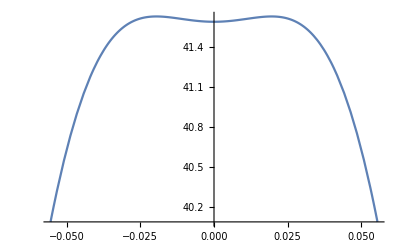

Bias field in x-direction (G): 41.5919

Gradient (G/cm): 0.

Curvature  (G/cm2): 0.042412

Power through coil (W): 77.4726

Voltage to be supplied (V): 12.9121

Resistance per coil (Ohm): 2.15202

Current per coil (A): 6

Inductance (H) : 0.0485216

Time constant (ms) : 22.547

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 222. | 236.616 | 8.12 | 90 | 111

```mathematica
Bias coils: Y (the medium ones)

(* wire spec *)
c = 0.812*10^-3 (* diameter of 20 AWG wire *);

(* geometry *)
R= 111*10^-3;
d= 111 *10^-3;
current = 6;
Nr = 9(*turns in the radial direction *);
Na = 10(* turns in the axial direction *);

Plot[BH[y, μ0, current, R, c, d, Nr, Na], {y, -d/2, d/2}] 

Print["Bias field in x-direction (G): " , BH[y, μ0, current, R, c, d, Nr, Na]/. y->0  ](* bias field in G *) 

Print["Gradient (G/cm): " , GradBH[y, μ0, current, R, c, d, Nr, Na]/100 /. y->0  ](* grad in G/cm *) 

Print["Curvature  (G/cm2): ",  CurvBH[y, μ0, current, R, c, d, Nr, Na]/10000 /. y->0 ](* grad in G/cm2 *) 

Print["Power through coil (W): ", powerAWG[current, Nr, Na, RAWG, R, c]]  (* power through coil in W *)

Print["Voltage to be supplied (V): ", voltageAWG[current, Nr, Na, RAWG, R, c]]  (* voltage in V *)

Print["Resistance per coil (Ohm): ", resistanceAWG[Nr, Na, RAWG, R, c]]  (* resistance in Ohm *)

Print["Current per coil (A): ", current]  (* current in A *)

Print["Inductance (H) : ", Inductance[ μ0, Nr, Na, R, c]] (* inductance of the coil in H *)

Print["Time constant (ms) : ", TimeConstAWG[μ0, Nr, Na, R, c, RAWG]*1000] (* time const in ms *)

TableForm[{{N[2*R]*1000, 2*(R+(c*Nr))*1000, c*Na*1000, Na*Nr, d*1000}},TableHeadings->{ {} ,{"Inner diameter (mm)", "Outer diameter (mm)", "Thickness (mm)", "# turns", "distance between coils (mm)"}}]
```

Bias (coils:ones smallest the Z)

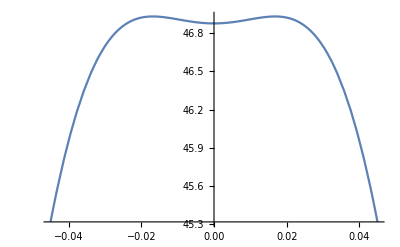

Bias field in x-direction (G): 46.8767

Gradient (G/cm): 5.68434×10^-16

Curvature  (G/cm2): 0.0783875

Power through coil (W): 49.0028

Voltage to be supplied (V): 9.80056

Inductance (H) : 0.0393812

Time constant (ms) : 20.0913

| Inner diameter (mm) | Outer diameter (mm) | Thickness (mm) | # turns | distance between coils (mm)
 | 180. | 196.24 | 8.12 | 100 | 90

```mathematica
Bias coils: Z (the smallest ones)

(* wire spec *)
c = 0.812*10^-3 (* diameter of 20 AWG wire *);

(* geometry *)
R= 90*10^-3;
d= 90 *10^-3;
current = 5;
Nr = 9(*turns in the radial direction *);
Na = 10(* turns in the axial direction *);

Plot[BH[y, μ0, current, R, c, d, Nr, Na], {y, -d/2, d/2}] 

Print["Bias field in x-direction (G): " , BH[y, μ0, current, R, c, d, Nr, Na]/. y->0  ](* bias field in G *) 

Print["Gradient (G/cm): " , GradBH[y, μ0, current, R, c, d, Nr, Na]/100 /. y->0  ](* grad in G/cm *) 

Print["Curvature  (G/cm2): ",  CurvBH[y, μ0, current, R, c, d, Nr, Na]/10000 /. y->0 ](* grad in G/cm2 *) 

Print["Power through coil (W): ", powerAWG[current, Nr, Na, RAWG, R, c]]  (* power through coil in W *)

Print["Voltage to be supplied (V): ", voltageAWG[current, Nr, Na, RAWG, R, c]]  (* voltage in V *)

Print["Inductance (H) : ", Inductance[ μ0, Nr, Na, R, c]] (* inductance of the coil in H *)

Print["Time constant (ms) : ", TimeConstAWG[μ0, Nr, Na, R, c, RAWG]*1000] (* time const in ms *)

TableForm[{{N[2*R]*1000, 2*(R+(c*Nr))*1000, c*Na*1000, Na*Nr, d*1000}},TableHeadings->{ {} ,{"Inner diameter (mm)", "Outer diameter (mm)", "Thickness (mm)", "# turns", "distance between coils (mm)"}}]
```